## NURBS Curve

```mathematica
curveKnots={0,0,0,.25,.5,.75,1,1,1};
curveCp={{-2.0,0.0,0.0,1.0},{0.0,0.0,0.0,1.0},{1.0,0.0,0.0,1.0},{2.0,0.0,1.3202035427093506,1.0},{0.9792511463165283,0.014374732971191406,1.8168606758117676,9.309999465942383},{-0.0020470619201660156,-0.3087310791015625,-0.42721521854400635,1.0}};
ToExpression[Import["/tmp/nurbs_curve.txt","String"]];
deriv1=(Arrow[{{#1,#2,#3},{#1,#2,#3}+{#4,#5,#6}/500}])&@@@crv;
Graphics3D[{
BSplineCurve[curveCp[[All,1;;3]],SplineDegree->2,SplineWeights->Flatten[curveCp[[All,4;;4]]]],
Red,Line[crv[[All,1;;3]]],
Green,deriv1,
PointSize[Medium],Red,Point[crv[[All,1;;3]]],
Gray,Line[curveCp[[All,1;;3]]]
}]
```

-Graphics3D-

## BSpline Surface

```mathematica
cpts=Table[{i,j,RandomReal[{-1,1}],RandomReal[{-1,1}]},{i,5},{j,5}];
```

```mathematica
surfKnots={0,0,0,0,.5,1,1,1,1};
cpts={{{1,1,-0.7417486553512296,1},{1,2,-0.8272445659579368,1},{1,3,0.056384039811391506,1},{1,4,-0.8565668867842464,1},{1,5,-0.027038808836199912,1}},{{2,1,-0.8954639917925951,1},{2,2,0.7766849857222553,1},{2,3,-0.2762882340944248,1},{2,4,0.18616037830975074,1},{2,5,-0.8933549711042139,1}},{{3,1,-0.4470460035460979,1},{3,2,-0.9258719097096733,1},{3,3,-0.5237670863586921,10},{3,4,0.11854173291263326,1},{3,5,0.9615924014809489,1}},{{4,1,0.9195532263713426,1},{4,2,-0.10327619833646784,1},{4,3,-0.16756710093868232,1},{4,4,0.7063963753875271,1},{4,5,-0.05516995763136112,1}},{{5,1,0.9561682326127552,1},{5,2,-0.500642765940114,1},{5,3,0.2473747081580262,1},{5,4,0.10467945795748923,1},{5,5,0.5112014481491505,1}}};
ToExpression[Import["/tmp/bspline_surf.txt","String"]];
surfpts=surf[[All,1;;3]];
surfU=(Arrow[{{#1,#2,#3},{#1,#2,#3}+{#4,#5,#6}/25}])&@@@surf;
surfV=(Arrow[{{#1,#2,#3},{#1,#2,#3}+{#7,#8,#9}/25}])&@@@surf;
b=Graphics3D[BSplineSurface[cpts,SplineDegree->3,SplineKnots->{surfKnots,surfKnots}]];
Show[Graphics3D[{
PointSize[Medium],Blue,Point[surfpts],
Gray,Line[cpts],Line[Transpose[cpts]],
Arrowheads[Small],Green,surfU,
Arrowheads[Small],Red,surfV,
}],b]
```

-Graphics3D-

```mathematica
surfU[[1]]
```

## BSpline Curve

```mathematica
curveKnots={0,0,0,.25,.5,.75,1,1,1};
curveCp={{-2.0,0.0,0.0,1.0},{0.0,0.0,0.0,1.0},{1.0,0.0,0.0,1.0},{2.0,0.0,1.3202035427093506,1.0},{0.9792511463165283,0.014374732971191406,1.8168606758117676,9.309999465942383},{-0.0020470619201660156,-0.3087310791015625,-0.42721521854400635,1.0}};
ToExpression[Import["/tmp/bspline_curve.txt","String"]];
deriv1=(Arrow[{{#1,#2,#3},{#1,#2,#3}+{#4,#5,#6}/50}])&@@@crv;
Graphics3D[{
BSplineCurve[curveCp[[All,1;;3]],SplineDegree->2],
Red,Line[crv[[All,1;;3]]],
Green,deriv1,
PointSize[Medium],Red,Point[crv[[All,1;;3]]],
Gray,Line[curveCp[[All,1;;3]]]
}]
```

-Graphics3D-

## BSpline Basis

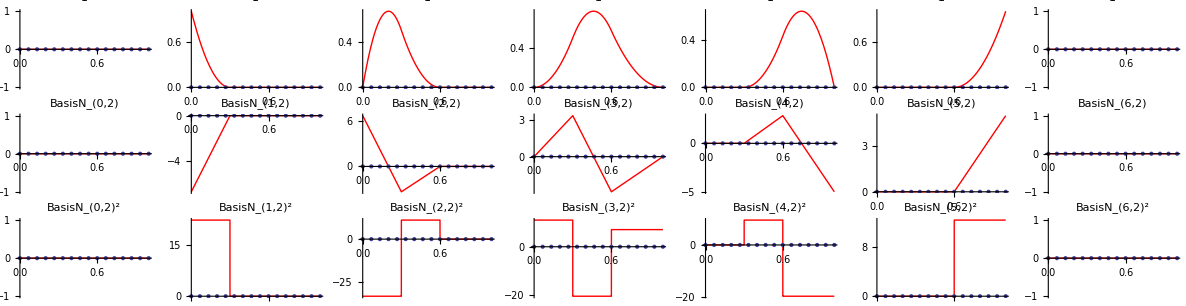

```mathematica
ToExpression[Import["/tmp/bspline_basis.txt","String"]]
GraphicsGrid[Table[Table[
Show[{
Plot[
D[BSplineBasis[{p,knots},i,x],{x,k}]/.x->xx,{xx,knots[[1]],knots[[numKnots-p]]},
PlotStyle->Red,
PlotLabel->Subscript[BasisN, i,p]^(k) ,
PlotRange->Full],
ListPlot[nn[i,p,k]]
}] 
,{i,0,numKnots-p-2}],{k,0,2}]
]
```

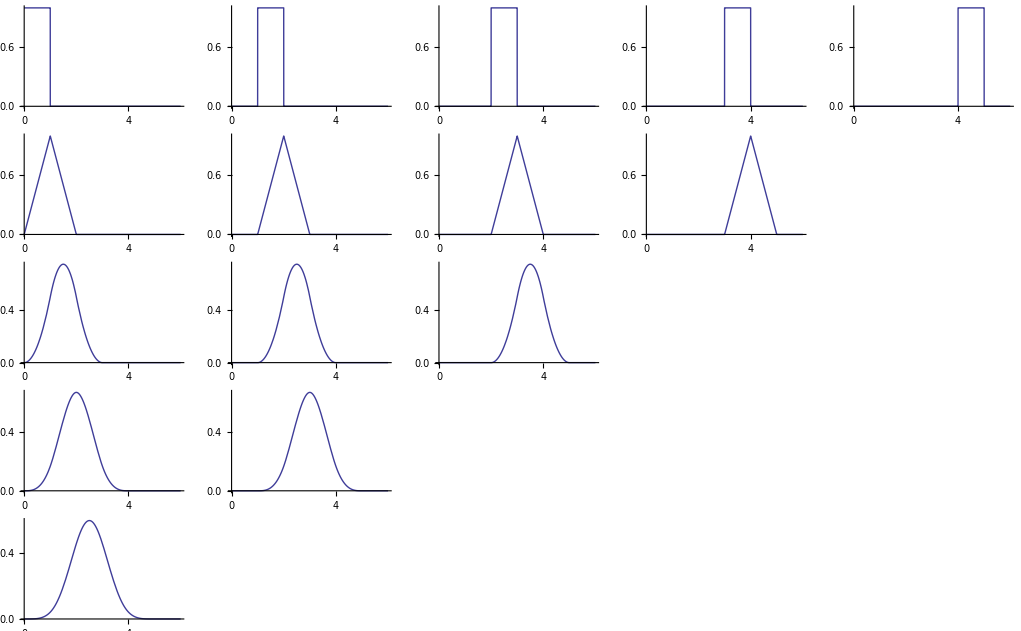

```mathematica
opp=5; knots=Table[i-1,{i,opp+1}];
GraphicsGrid[Table[Table[
Plot[BSplineBasis[{d,knots},i,x],{x,0,opp+1}]
,{i,0,opp-d-1}],{d,0,opp-1}]]
```